```mathematica
gpatFunctions={plus,times,atan,sin, gauss};
(*gpFunctions={abs,plus,minus,times,div,mod,atan,cos,sin, gauss,gaussdif};*)
gpFunctions={plus,times,atan,sin, gauss};
```

```mathematica
readBSFGenome[fileName_]:= 
Module[{exp},
exp=ToExpression[StringSplit[Import[fileName],"\n"]]⟦-1,1,1⟧;
exp
]
```

```mathematica
computeFunctionRatios[genome_, functions_]:=
Module[{counts,total},
counts=Length[Position[genome,#]]&/@functions;
total=Total[counts];
If[total==0,counts,counts/total]
]
```

```mathematica
computeAverageFunctionRatios[dir_,functions_]:=
Module[{},
Mean[computeFunctionRatios[readBSFGenome[#],functions]&/@FileNames["*O_GENOMES_MATH.txt",dir]]
]
```

```mathematica
plotAverageFunctionRatios[dir_,functions_]:=BarChart[computeAverageFunctionRatios[dir,functions],ChartStyle->"Rainbow",ChartLegends->functions]
```

```mathematica
computeFunctionRatios[bsfGenome,gpatFunctions]
```

{1/5,2/5,1/5,0,1/5}

```mathematica
avgRatios=computeAverageFunctionRatios["~/java/exp/GPAT/",gpatFunctions]
```

{71/250,737/1500,29/500,1/30,2/15}

```mathematica
List/@avgRatios
```

{{71/250},{737/1500},{29/500},{1/30},{2/15}}

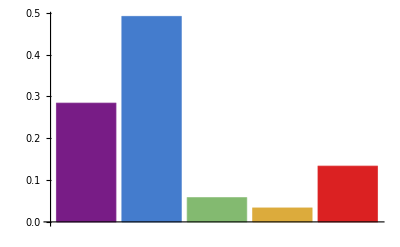
-Graphics--Graphics- | plus
-Graphics- | times
-Graphics- | atan
-Graphics- | sin
-Graphics- | gauss

```mathematica
plotAverageFunctionRatios["~/java/exp/GPAT/",gpatFunctions]
```

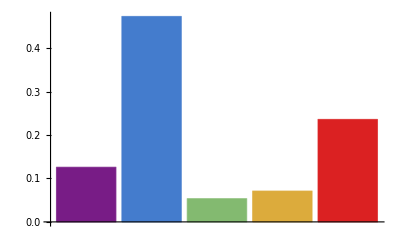
-Graphics--Graphics- | plus
-Graphics- | times
-Graphics- | atan
-Graphics- | sin
-Graphics- | gauss

```mathematica
plotAverageFunctionRatios["~/java/exp/GP/",gpFunctions]
```